```mathematica
(*对重子图进行各种贡献画图*)
```

```mathematica
(*先对ud两个夸克的贡献对于不同的图画，此时只考虑核子-pi channel*)
(*this is for diagram b*)
```

```mathematica
(*输入系数*)
```

```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
ct=(3*c2+c1)/3;
c4=4c1;
Cc=-2Dc;
```

```mathematica
(*Import the calculation result,d is delta*)
```

```mathematica
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-n-dleta-up-xi1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;
dHdau=Query[1,3]@dgpdu;
dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;
dEdau=Query[2,3]@dgpdu;
dHdgfu=Interpolation[Flatten[dHdgu,1]];
dHerfu=Interpolation[Flatten[dHeru,1]];

dEdgfu=Interpolation[Flatten[dEdgu,1]];
dEerfu=Interpolation[Flatten[dEeru,1]];
```

```mathematica
dgpdd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-n-dleta-dp-xi1.wdx"];
dHdgd=Query[1,1]@dgpdd;
dHerd=Query[1,2]@dgpdd;
dHdad=Query[1,3]@dgpdd;
dEdgd=Query[2,1]@dgpdd;
dEerd=Query[2,2]@dgpdd;
dEdad=Query[2,3]@dgpdd;
dHdgfd=Interpolation[Flatten[dHdgd,1]];
dHerfd=Interpolation[Flatten[dHerd,1]];

dEdgfd=Interpolation[Flatten[dEdgd,1]];
dEerfd=Interpolation[Flatten[dEerd,1]];
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-n-up-xi1.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgfu=Interpolation[Flatten[Hdgu,1]];
Herfu=Interpolation[Flatten[Heru,1]];
Hdafu=Interpolation[Flatten[Hdau,1]];
Edgfu=Interpolation[Flatten[Edgu,1]];
Eerfu=Interpolation[Flatten[Eeru,1]];
Edafu=Interpolation[Flatten[Edau,1]];
```

```mathematica
gpdd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-n-dp-xi1.wdx"];
Hdgd=Query[1,1]@gpdd;
Herd=Query[1,2]@gpdd;
Hdad=Query[1,3]@gpdd;
Edgd=Query[2,1]@gpdd;
Eerd=Query[2,2]@gpdd;
Edad=Query[2,3]@gpdd;
Hdgfd=Interpolation[Flatten[Hdgd,1]];
Herfd=Interpolation[Flatten[Herd,1]];
Hdafd=Interpolation[Flatten[Hdad,1]];
Edgfd=Interpolation[Flatten[Edgd,1]];
Eerfd=Interpolation[Flatten[Eerd,1]];
Edafd=Interpolation[Flatten[Edad,1]];
```

```mathematica
Dtermu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-n-D-up-xi1.wdx"];
HerDu=Query[1,1]@Dtermu;
HdaDu=Query[1,2]@Dtermu;

EerDu=Query[2,1]@Dtermu;
EdaDu=Query[2,2]@Dtermu;
HerDfu=Interpolation[Flatten[HerDu,1]];
HdaDfu=Interpolation[Flatten[HdaDu,1]];

EerDfu=Interpolation[Flatten[EerDu,1]];
EdaDfu=Interpolation[Flatten[EdaDu,1]];
```

```mathematica
Dtermd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-n-D-dp-xi1.wdx"];
HerDd=Query[1,1]@Dtermd;
HdaDd=Query[1,2]@Dtermd;

EerDd=Query[2,1]@Dtermd;
EdaDd=Query[2,2]@Dtermd;
HerDfd=Interpolation[Flatten[HerDd,1]];
HdaDfd=Interpolation[Flatten[HdaDd,1]];

EerDfd=Interpolation[Flatten[EerDd,1]];
EdaDfd=Interpolation[Flatten[EdaDd,1]];
```

```mathematica
deDtermd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-n-dleta-D-dp-xi1.wdx"];
deHerDd=Query[1,1]@deDtermd;

deEerDd=Query[2,1]@deDtermd;
deHerDfd=Interpolation[Flatten[deHerDd,1]];
deEerDfd=Interpolation[Flatten[deEerDd,1]];
```

```mathematica
deDtermu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-n-dleta-D-up-xi1.wdx"];
deHerDu=Query[1,1]@deDtermu;

deEerDu=Query[2,1]@deDtermu;
deHerDfu=Interpolation[Flatten[deHerDu,1]];
deEerDfu=Interpolation[Flatten[deEerDu,1]];
```

```mathematica
Hdgf1u[x_,t_]:=Chop[Hdgfu[x,t],10^-7];
Herf1u[x_,t_]:=Chop[Herfu[x,t],10^-7]+Chop[Hdafu[x,t],10^-7];
Edgf1u[x_,t_]:=Chop[Edgfu[x,t],10^-7];
Eerf1u[x_,t_]:=Chop[Eerfu[x,t],10^-7]+Chop[Edafu[x,t],10^-7];
```

```mathematica
Hdgf1d[x_,t_]:=Chop[Hdgfd[x,t],10^-7];
Herf1d[x_,t_]:=Chop[Herfd[x,t],10^-7]+Chop[Hdafd[x,t],10^-7];
Edgf1d[x_,t_]:=Chop[Edgfd[x,t],10^-7];
Eerf1d[x_,t_]:=Chop[Eerfd[x,t],10^-7]+Chop[Edafd[x,t],10^-7];
```

```mathematica
HerDf1d[x_,t_]:=Chop[HerDfd[x,t],10^-7]+Chop[HdaDfd[x,t],10^-7];EerDf1d[x_,t_]:=Chop[EerDfd[x,t],10^-7]+Chop[EdaDfd[x,t],10^-7];
```

```mathematica
HerDf1u[x_,t_]:=Chop[HerDfu[x,t],10^-7]+Chop[HdaDfu[x,t],10^-7];EerDf1u[x_,t_]:=Chop[EerDfu[x,t],10^-7]+Chop[EdaDfu[x,t],10^-7];
```

```mathematica
(*original result fron the calculation*)
```

```mathematica
Hdgfnu[x_,t_]:=Hdgf1u[x,t]+dHdgfu[x,t];
Herfnu[x_,t_]:=Herf1u[x,t]+dHerfu[x,t]+HerDf1u[x,t]+deHerDfu[x,t];
Edgfnu[x_,t_]:=Edgf1u[x,t]+dEdgfu[x,t];
Eerfnu[x_,t_]:=Eerf1u[x,t]+dEerfu[x,t]-EerDf1u[x,t]-deEerDfu[x,t];
```

```mathematica
Hdgfnd[x_,t_]:=Hdgf1d[x,t]+dHdgfd[x,t];
Herfnd[x_,t_]:=Herf1d[x,t]+dHerfd[x,t]+HerDf1d[x,t]+deHerDfd[x,t];
Edgfnd[x_,t_]:=Edgf1d[x,t]+dEdgfd[x,t];
Eerfnd[x_,t_]:=Eerf1d[x,t]+dEerfd[x,t]-EerDf1d[x,t]-deEerDfd[x,t];
```

```mathematica
(*result of Δ+ pi0 as input without coe 作为十重态计算中的基础GPD组合*)
```

```mathematica
Hdgud[x_,t_]:=((4/3)Hdgfnu[x,t]-(2/3)Hdgfnd[x,t]);
Herud[x_,t_]:=((4/3)Herfnu[x,t]-(2/3)Herfnd[x,t]);
Edgud[x_,t_]:=((4/3)Edgfnu[x,t]-(2/3)Edgfnd[x,t]);
Eerud[x_,t_]:=((4/3)Eerfnu[x,t]-(2/3)Eerfnd[x,t]);

Hdgdd[x_,t_]:=((2/3)Hdgfnu[x,t]-(1/3)Hdgfnd[x,t]);
Herdd[x_,t_]:=((2/3)Herfnu[x,t]-(1/3)Herfnd[x,t]);
Edgdd[x_,t_]:=((2/3)Edgfnu[x,t]-(1/3)Edgfnd[x,t]);
Eerdd[x_,t_]:=((2/3)Eerfnu[x,t]-(1/3)Eerfnd[x,t]);
```

```mathematica
(*result of Δ+(D1) pi0 as input*)
```

```mathematica
(*E has extra coe*)
```

```mathematica
D1Coe=(1/(2*(2π)^4))*(-I)*((Cc)^2/(3fc^2));
(*upper pCoe is the coe in spf which do not include in calc*)
```

```mathematica
Eu=1.6699999468721227;
Ed=-2.029999921595019;
```

```mathematica
EuD=(4/3)Eu-(2/3)Ed;
EdD=(2/3)Eu-(1/3)Ed;
```

```mathematica
coD1u=2ct/(EuD);
coD1d=ct/EdD;
coD1s=0;
```

```mathematica
tdHdgu[x_,t_]:=D1Coe*((4/3)Hdgfnu[x,-t]-(2/3)Hdgfnd[x,-t]);
tdHeru[x_,t_]:=D1Coe*((4/3)Herfnu[x,-t]-(2/3)Herfnd[x,-t]);
tdEdgu[x_,t_]:=D1Coe*coD1u*((4/3)Edgfnu[x,-t]-(2/3)Edgfnd[x,-t]);
tdEeru[x_,t_]:=D1Coe*coD1u*((4/3)Eerfnu[x,-t]-(2/3)Eerfnd[x,-t]);

tdHdgd[x_,t_]:=D1Coe*((2/3)Hdgfnu[x,-t]-(1/3)Hdgfnd[x,-t]);
tdHerd[x_,t_]:=D1Coe*((2/3)Herfnu[x,-t]-(1/3)Herfnd[x,-t]);
tdEdgd[x_,t_]:=D1Coe*coD1d*((2/3)Edgfnu[x,-t]-(1/3)Edgfnd[x,-t]);
tdEerd[x_,t_]:=D1Coe*coD1d*((2/3)Eerfnu[x,-t]-(1/3)Eerfnd[x,-t]);
```

```mathematica
(*pi+ Δ0*)
```

```mathematica
d0Coe=(1/(2*(2π)^4))*(-I)*((Cc)^2/(6fc^2));
```

```mathematica
coD0u=ct/(EdD);
coD0d=2ct/EuD;
coD0s=0;
```

```mathematica
d0Hdgu[x_,t_]:=d0Coe*Hdgdd[x,-t];
d0Heru[x_,t_]:=d0Coe*Herdd[x,-t];
d0Edgu[x_,t_]:=d0Coe*coD0u*Edgdd[x,-t];
d0Eeru[x_,t_]:=d0Coe*coD0u*Eerdd[x,-t];

d0Hdgd[x_,t_]:=d0Coe*Hdgud[x,-t];
d0Herd[x_,t_]:=d0Coe*Herud[x,-t];
d0Edgd[x_,t_]:=d0Coe*coD0d*Edgud[x,-t];
d0Eerd[x_,t_]:=d0Coe*coD0d*Eerud[x,-t];
```

```mathematica
(*result of pi- Δ++ as input*)
```

```mathematica
d2Coe=(1/(2*(2π)^4))*(-I)*((Cc)^2/(2fc^2));
```

```mathematica
coD2u=3ct/(EuD+EdD);
coD2d=0;
coD2s=0;
```

```mathematica
dHdgu2[x_,t_]:=d2Coe*(Hdgud[x,-t]+Hdgdd[x,-t]);
dHeru2[x_,t_]:=d2Coe*(Herud[x,-t]+Herdd[x,-t]);
dEdgu2[x_,t_]:=d2Coe*coD2u*(Edgud[x,-t]+Edgdd[x,-t]);
dEeru2[x_,t_]:=d2Coe*coD2u*(Eerud[x,-t]+Eerdd[x,-t]);
```

```mathematica
(*whole result*)
```

```mathematica
Hdguall[x_,t_]:=tdHdgu[x,t]+d0Hdgu[x,t]+dHdgu2[x,t];
Heruall[x_,t_]:=tdHeru[x,t]+d0Heru[x,t]+dHeru2[x,t];
Edguall[x_,t_]:=tdEdgu[x,t]+d0Edgu[x,t]+dEdgu2[x,t];
Eeruall[x_,t_]:=tdEeru[x,t]+d0Eeru[x,t]+dEeru2[x,t];

Hdgdall[x_,t_]:=tdHdgd[x,t]+d0Hdgd[x,t];
Herdall[x_,t_]:=tdHerd[x,t]+d0Herd[x,t];
Edgdall[x_,t_]:=tdEdgd[x,t]+d0Edgd[x,t];
Eerdall[x_,t_]:=tdEerd[x,t]+d0Eerd[x,t];
```

```mathematica
pHu=Show[Plot3D[Hdguall[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Heruall[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["H_u",Black,30,FontFamily->Times],Scaled[{1.16,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
pEu=Show[Plot3D[Edguall[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Eeruall[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["E_u",Black,30,FontFamily->Times],Scaled[{1.22,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
pHd=Show[Plot3D[Hdgdall[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Herdall[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["H_d",Black,30,FontFamily->Times],Scaled[{1.16,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
pEd=Show[Plot3D[Edgdall[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Re[Eerdall[x,t]],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["E_d",Black,30,FontFamily->Times],Scaled[{1.18,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*pathHu=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\baryon\\51",
"Hu-c.pdf"}];
pathEu=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\baryon\\51",
"Eu-c.pdf"}];
```

```mathematica
(*Export[pathHu,pHu]
Export[pathEu,pEu]
```

```mathematica
(*pathHd=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\baryon\\51",
"Hd-c.pdf"}];
pathEd=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\baryon\\51",
"Ed-c.pdf"}];
```

```mathematica
(*Export[pathHd,pHd]
Export[pathEd,pEd]
```

```mathematica
Hdguall2[x_,t_]:=x*(pHdgu[x,t]+nHdgu[x,t]);
Heruall2[x_,t_]:=x*(pHeru[x,t]+nHeru[x,t]);
Edguall2[x_,t_]:=x*(pEdgu[x,t]+nEdgu[x,t]);
Eeruall2[x_,t_]:=x*(pEeru[x,t]+nEeru[x,t]);

Hdgdall2[x_,t_]:=x*(pHdgd[x,t]+nHdgd[x,t]);
Herdall2[x_,t_]:=x*(pHerd[x,t]+nHerd[x,t]);
Edgdall2[x_,t_]:=x*(pEdgd[x,t]+nEdgd[x,t]);
Eerdall2[x_,t_]:=x*(pEerd[x,t]+nEerd[x,t]);
```

```mathematica
pHu2=Show[Plot3D[Hdguall2[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Heruall2[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["xH_u",Black,30,FontFamily->Times],Scaled[{1.16,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
pEu2=Show[Plot3D[Edguall2[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Re[Eeruall2[x,t]],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["xE_u",Black,30,FontFamily->Times],Scaled[{1.22,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
pHd2=Show[Plot3D[Hdgdall2[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Herdall2[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["xH_d",Black,30,FontFamily->Times],Scaled[{1.16,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
pEd2=Show[Plot3D[Edgdall2[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Re[Eerdall2[x,t]],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["xE_d",Black,30,FontFamily->Times],Scaled[{1.18,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*pathHu2=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\baryon\\51",
"Hu2-c.pdf"}];
pathEu2=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\baryon\\51",
"Eu2-c.pdf"}];
Export[pathHu2,pHu2]
Export[pathEu2,pEu2]
```

```mathematica
(*pathHd2=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\baryon\\51",
"Hd2-c.pdf"}];
pathEd2=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\baryon\\51",
"Ed2-c.pdf"}];
Export[pathHd2,pHd2]
Export[pathEd2,pEd2]
```

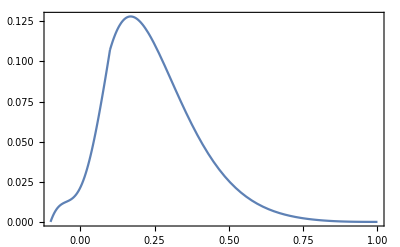
-Graphics-H_dxdiagram n

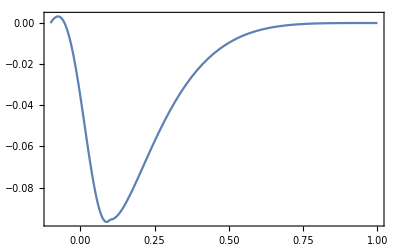
-Graphics-E_dxdiagram n

```mathematica
pHd2d=Labeled[Show[Plot[Hdgdall[x,1],{x,0.1,1},PlotRange->All],Plot[Herdall[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d","x","diagram n"},{Left,Bottom,Top},LabelStyle->24]
pEd2d=Labeled[Show[Plot[Edgdall[x,1],{x,0.1,1},PlotRange->All],Plot[Eerdall[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d","x","diagram n"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
pathu=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"u-diagram-n.wdx"}];
pathd=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"d-diagram-n.wdx"}];
outu=<|"H"-><|"DG"->Hdguall[x,t],"ER"->Heruall[x,t]|>,"E"-><|"DG"->Edguall[x,t],"ER"->Eeruall[x,t]|>|>;
outd=<|"H"-><|"DG"->Hdgdall[x,t],"ER"->Herdall[x,t]|>,"E"-><|"DG"->Edgdall[x,t],"ER"->Eerdall[x,t]|>|>;
Export[pathu,outu]
Export[pathd,outd]
```

G:\calc-online\gpd\drawpic\baryon\gpd\result\u-diagram-n.wdx

G:\calc-online\gpd\drawpic\baryon\gpd\result\d-diagram-n.wdx